```mathematica
Remove["Global`*"]
```

```mathematica
(* This script calculates the distances of a given stiffness C tetrad to its *)
(* projections Subscript[C, i]=Subscript[P, i].C onto 7 of the 8 symmetry classes of elasticity (every C is trclinic) *)
(* The distance is defined as d=1-|Subscript[C, i]|/|C|, being 0 if C falls into the symmetry class i and *)
(* not exceeding 1. As the axes of anisotropy are unknown, d is minimized over the rotation. *)

(* Detailes can be found in M.Weber, R.Glüge, and A.Bertram. Distance of a stiffness tetrad *)
(* to the symmetry classes of linear elasticity. International Journal of Solids and Structures, *)
(* 156-157:281--293,2019. https://doi.org/10.1016/j.ijsolstr.2018.08.021 *)

(* Input: 6x6 stiffness Matrix w.r.t. the 6-dimensional non-normalized symmetric tensor basis with the ordering following Cowin (11,22,33,12,13,23) *)
(* Run with "Evaluation" -> "Evaluate Notebook" *)
(* Output: Bar-chart of the distances *)


(* Input: *)
(* Example: a monoclinic stiffness *)
K66={{47344.5,14639.4,14639.4,-622.211,-622.175,-1439.37},
{14639.4,39515.5,12773.5,4385.7,668.875,-2304.24},
{14639.4,12773.5,39515.5,668.931,4385.75,-2304.15},
{-622.211,4385.7,668.931,15690.,-3312.97,-1811.98},
{-622.175,668.875,4385.75,-3312.97,15690.1,-1811.92},
{-1439.37,-2304.24,-2304.15,-1811.98,-1811.92,18908.3}};

(* Example: a cubic stiffness *)
(*K66={{5,4,4,0,0,0},
{4,5,4,0,0,0},
{4,4,5,0,0,0},
{0,0,0,6,0,0},
{0,0,0,0,6,0},
{0,0,0,0,0,6}};
*)
(* Utility functions *)
T8Rayleigh[T2_]:=Table[T2[[i,m]]T2[[j,n]]T2[[k,o]] T2[[l,p]],{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,3},{n,1,3},{o,1,3},{p,1,3}];
T8T4[T8_,T4_]:=Table[Sum[T8[[m,n,o,p,i,j,k,l]]T4[[i,j,k,l]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}],  {m,1,3},{n,1,3},{o,1,3},{p,1,3}];
T8T8[T8_,T82_]:=Table[Sum[T8[[m,n,o,p,i,j,k,l]]T82[[i,j,k,l,q,r,s,t]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}],  {m,1,3},{n,1,3},{o,1,3},{p,1,3},{q,1,3},{r,1,3},{s,1,3},{t,1,3}];
T4T4[T4_,T42_]:=Sum[T4[[i,j,k,l]]T42[[i,j,k,l]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
ScalarProdT4[T4_]:=T4T4[T4,T4];
Translate66to3333[M66_]:=(Indexmatrix={{1,4,5},{4,2,6},{5,6,3}};
Faktormatrix={{1,1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],1,1/Sqrt[2]},{1/Sqrt[2],1/Sqrt[2],1}};
Table[M66[[Indexmatrix[[i,j]],Indexmatrix[[k,l]]]]*Faktormatrix[[i,j]]*Faktormatrix[[k,l]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}])
Translate3333to66[C3333_]:=(Ivek1={1,2,3,1,1,2};
Ivek2={1,2,3,2,3,3};
Faktvek={1,1,1,Sqrt[2],Sqrt[2],Sqrt[2]};
Table[C3333[[Ivek1[[i]],Ivek2[[i]],Ivek2[[j]],Ivek1[[j]]]]*Faktvek[[i]]*Faktvek[[j]],{i,1,6},{j,1,6}])
id=IdentityMatrix[3];
```

```mathematica
(* Parametrizing the rotation *)
(* R: 2nd order rotation tensor depending on three Euler angles *)
(* We choose the extrinsic rotations (i.e. w.r.t. fixed axes) in the order z,y,x around the angles alpha, beta, gamma, respectively. *)
(* The intervals of the Euler angles are: 
  -Pi < alpha ≤ Pi 
-Pi/2 ≤ beta ≤ Pi/2
-Pi < gamma < Pi*)
(* With this choice, simplifications regarding the angle gamma are possible for the monoclinic and transversal symmetries
with the generators that are used here. The distance function becomes gamma-invariant, and a minimization over alpha and beta 
is sufficient, see the appending cells and also Çağri, Kochetov, Slawinski: Identifying Symmetry Classes of Elasticity Tensors 
Using Monoclinic Distance Function, Journal of Elasticity (2011), 102(2):175-190. *)

R=RotationMatrix[gamma,{1,0,0}].RotationMatrix[beta,{0,1,0}].RotationMatrix[alpha,{0,0,1}];

(* Rot: 8th order rotation tensor that, when applied to a fourth order tensor K, gives the generalized rotation (Rayleigh product) of R with K *) 
Rot=T8Rayleigh[R];
```

```mathematica
(* The generators of the 6 discrete symmetry groups monoclinic, orthotropic, tetragonal, trigonal, hexagonal, cubic*)
SymGroups={};
AppendTo[SymGroups,{-id+{{2,0,0},{0,0,0},{0,0,0}}}]; (*1 monoclinic *)
AppendTo[SymGroups,{-id+{{2,0,0},{0,0,0},{0,0,0}},-id+{{0,0,0},{0,2,0},{0,0,0}}}]; (*2 orthotropic *)
AppendTo[SymGroups,{{{0,1,0},{-1,0,0},{0,0,1}},-id+{{2,0,0},{0,0,0},{0,0,0}}}]; (*3 tetragonal *)
AppendTo[SymGroups,{RotationMatrix[2*Pi/3,{0,0,1}],RotationMatrix[Pi,{0,1,0}]}];  (*4 trigonal *)
AppendTo[SymGroups,{RotationMatrix[Pi/3,{1,0,0}],-id+{{0,0,0},{0,0,0},{0,0,2}}}];  (*5 hexagonal *)
AppendTo[SymGroups,{{{1,0,0},{0,0,1},{0,-1,0}},{{0,0,1},{1,0,0},{0,1,0}}}]; (*6 cubic *)

(* Prepare empty list to hold the projectors onto the symmetry groups*)
P8s={};

(* We combine the group elements until no new group members appear and build then the projectors by averaging over all group members *)
For[iouter=1,iouter≤6,iouter++,
Print["Building symmetry group ",iouter, " and projector"];
list=SymGroups[[iouter]];
init=Length[list];
outit=100000; 
(* Generate all elements in symmetry group, proceed while new elements appear *)
While[init≠outit,
init=Length[list];
For[i=1,i≤init,i+=1,
For[j=1,j≤init,j+=1,
list=Append[list,FullSimplify[list[[i]].list[[j]]]]
];
];
list=DeleteDuplicates[list];
outit=Length[list];
];
(* Build 8th order projector by summing over all group elements *)
AppendTo[P8s,FullSimplify[1/Length[list]Sum[T8Rayleigh[list[[x]]],{x,1,Length[list]}]]];
];
```

Building symmetry group 1 and projector

Building symmetry group 2 and projector

Building symmetry group 3 and projector

Building symmetry group 4 and projector

Building symmetry group 5 and projector

Building symmetry group 6 and projector

```mathematica
(* Initialize empty list that holds the distances later on *)
distances={};
(* Cast input to fourth order tensor *)
K=Translate66to3333[K66];

(* Loop over the 6 non-trivial discrete symmetry groups *)
For[iouter=1,iouter≤6,iouter++,
Print["Minimization ", iouter , " of 6."];
(* Combine P8 und Rot *)
SuperP=T8T8[P8s[[iouter]],Rot];
objectivefunction=ScalarProdT4[T8T4[Rot,K]-T8T4[SuperP,K]];

(* The method "RandomSearch" starts a local minimization from all grid points. 
With the grid spacing no larger than Pi/4, the global minimum is found, since 
no symmetries higher than a four-fold rotational symmetry 
can be distinguished in linear elasticity. *)

ni=4;nj=2;nk=4; (* alpha (2Pi), beta (Pi) and gamma (2Pi) interval division *)
If[iouter==1  || iouter==5, (* in case of monoclinic and transversal isotropic symmetry a two-dimensional search domain suffices, see appending cells *)
res=NMinimize[{objectivefunction/.{gamma->0},-Pi≤alpha≤Pi,-Pi/2≤beta≤Pi/2},{alpha,beta},Method->{"RandomSearch","InitialPoints"->Flatten[Table[{-Pi+i*2Pi/ni,-Pi/2+j*Pi/nj},{i,1,ni},{j,1,nj}],1]}],
res=NMinimize[{objectivefunction,-Pi≤alpha≤Pi,-Pi/2≤beta≤Pi/2,-Pi≤gamma≤Pi},{alpha,beta,gamma},Method->{"RandomSearch","InitialPoints"->Flatten[Table[{-Pi+i*2Pi/ni,-Pi/2+j*Pi/nj,-Pi+k*2Pi/nk},{i,1,ni},{j,1,nj},{k,1,nk}],2]}]
]; 
(* The method "NelderMead" is much faster, but may not give the global minimum. *)
(*erg=NMinimize[{objectivefunction,-Pi≤alpha≤Pi,-Pi/2≤beta≤Pi/2,-Pi≤gamma≤Pi},{alpha,beta,gamma},Method->{"NelderMead"}];*)
AppendTo[distances,Sqrt[res[[1]]]/Sqrt[ScalarProdT4[K]]];
];
```

Minimization 1 of 6.

Minimization 2 of 6.

Minimization 3 of 6.

Minimization 4 of 6.

Minimization 5 of 6.

Minimization 6 of 6.

```mathematica
(* Add distance to isotropy using isotropic projectors *)
P1=Table[1/3id[[i,j]]id[[k,l]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
P2=Table[1/2(id[[i,k]]id[[j,l]]+id[[i,l]]id[[j,k]]),{i,1,3},{j,1,3},{k,1,3},{l,1,3}]-P1;
KISO=T4T4[K,P1]P1+1/5T4T4[K,P2]P2;
AppendTo[distances,Sqrt[ScalarProdT4[K-KISO]/ScalarProdT4[K]]];
```

{monoclinic
0.,orthotropic
11.3,tetragonal
12.6,trigonal
8.6,hex./trans.-iso.
14.6,cubic
14.2,isotropic
21.5}

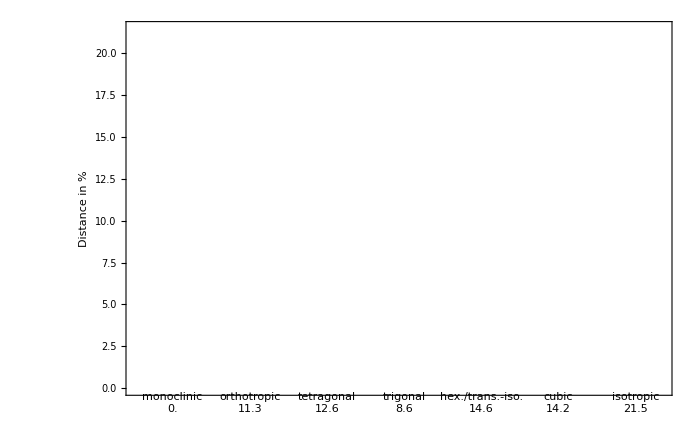

logo.svg

```mathematica
(* Draw chart *)
strings={"monoclinic","orthotropic","tetragonal","trigonal","hex./trans.-iso.","cubic","isotropic"};
dists=Table[ToString[100Round[distances[[i]],0.001]],{i,1,7}];
strs=Table[StringJoin[strings[[i]],"\n",dists[[i]]],{i,1,7}]
barchart=BarChart[100distances,BarSpacing->{0.5,2},ChartLabels->{Placed[strs,Below]},ChartStyle->{White},Epilog->{Text[MatrixForm[K66],{3.3,18}]},Frame->True,FrameLabel->{None,Style["Distance in %",Black]},BaseStyle->{Thick,FontSize->14},AxesStyle->Black, LabelStyle->Black,FrameStyle->Bold,ImageSize->700]
Export["logo.svg",barchart]
```

```mathematica
(* A P P E N D I X   C E L L   1   -   Demonstration of the interaction of R and P in special cases - part 1 - monoclinic symmetry *)

(* Simplifications regarding the angle gamma are possible for the monoclinic generator that has been used here. 
The distance function becomes gamma-invariant, and a minimization over alpha and beta is sufficient. *)

SuperP=T8T8[P8s[[1]],Rot]; (* Load monoclinic projector *)
K66={{6,5,4,3,2,1},{5,9,5,4,3,2},{4,5,7,1,2,3},{3,4,1,5,3,2},{2,3,2,3,8,1},{1,2,3,2,1,7}}; (* Triclinic stiffness *)
K=Translate66to3333[K66];
K=K/Sqrt[ScalarProdT4[K]]; (* Normalize for simplicity *)
objectivefunction=ScalarProdT4[T8T4[Rot,K]-T8T4[SuperP,K]];

ContourPlot3D[objectivefunction,{alpha,-Pi,Pi},{beta,-Pi/2,Pi/2},{gamma,-Pi,Pi},Contours->{0.04,0.08,0.12},ContourStyle->{Directive[Opacity[0.3],Red],Directive[Opacity[0.2],Red],Directive[Opacity[0.1],Red]},Mesh->None,PlotPoints->{20,10,2},MaxRecursion->0,BoxRatios->{2, 1,2}]
```

-Graphics3D-

```mathematica
(* A P P E N D I X   C E L L   2   -   Demonstration of the interaction of R and P in special cases - part 2 - transversal isotropy *)

(* Simplifications regarding the angle gamma are possible for the hexagonal generator (indistinguishable from transversal isotropy in elasticity) that has been used here. 
The distance function becomes gamma-invariant, and a minimization over alpha and beta is sufficient. *)

SuperP=T8T8[P8s[[5]],Rot]; (* Load transversal isotropic projector *)
K66={{6,5,4,3,2,1},{5,9,5,4,3,2},{4,5,7,1,2,3},{3,4,1,5,3,2},{2,3,2,3,8,1},{1,2,3,2,1,7}}; (* Triclinic stiffness *)
K=Translate66to3333[K66];
K=K/Sqrt[ScalarProdT4[K]];(* Normalize for simplicity *)
objectivefunction=ScalarProdT4[T8T4[Rot,K]-T8T4[SuperP,K]];

ContourPlot3D[objectivefunction,{alpha,-Pi,Pi},{beta,-Pi/2,Pi/2},{gamma,-Pi,Pi},Contours->3*{0.04,0.08,0.12},ContourStyle->{Directive[Opacity[0.3],Red],Directive[Opacity[0.2],Red],Directive[Opacity[0.1],Red]},Mesh->None,PlotPoints->{10,5,10},MaxRecursion->0,BoxRatios->{2, 1,2}]
```

-Graphics3D-

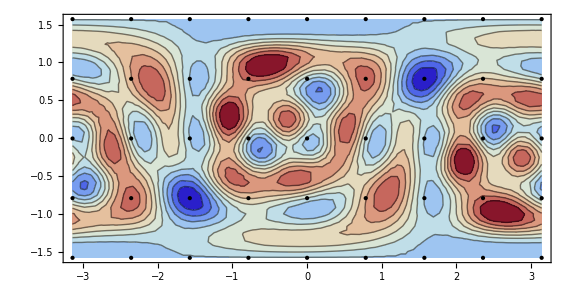

-Graphics3D-

```mathematica
(* A P P E N D I X   C E L L   3   -   Number of grid points necessary to obtain the global minimum *)

(* The worst possible case is the determination of the distance of a triclinic cell to the monoclinic symmetry. 
Then the global minimum is only two-fold, as the monoclinic symmetry group is of order two. Less global minima
are not possible. Using the result from Appendix Cell 1, we draw grid points and the distance landscape in one plot to see that a grid 
spacing of Pi/4 is sufficient. Then, each local minimum has at least one grid point, such that each local minimum is attained
at least once. However, a better discretization of the orientation space than with two Euler angles would be through a fair distribution of points on the sphere 
(see second plot). In case of three Euler angles, unit quaternions or platonic solids may give a good starting point distribution (see, e.g. Nawratil and Pottmann: 
Subdivision Schemes for the fair Discretization of the Spherical Motion Group, Journal of Computational and Applied Mathematics (2008), 222(2), 574-591). *)

SuperP=T8T8[P8s[[1]],Rot]; (* Load monoclinic projector *)
K66={{47344.5,14639.4,14639.4,-622.211,-622.175,-1439.37},{14639.4,39515.5,12773.5,4385.7,668.875,-2304.24},{14639.4,12773.5,39515.5,668.931,4385.75,-2304.15},{-622.211,4385.7,668.931,15690.,-3312.97,-1811.98},{-622.175,668.875,4385.75,-3312.97,15690.1,-1811.92},{-1439.37,-2304.24,-2304.15,-1811.98,-1811.92,18908.3}}; (* Triclinic stiffness *)
K=Translate66to3333[K66];
K=K/Sqrt[ScalarProdT4[K]];(* Normalize for simplicity *)
objectivefunction=ScalarProdT4[T8T4[Rot,K]-T8T4[SuperP,K]];
gridspacing=Pi/4;
Show[ContourPlot[objectivefunction/.{gamma->0},{alpha,-Pi,Pi},{beta,-Pi/2,Pi/2},Mesh->None,Contours->10,PlotPoints->{40,20},MaxRecursion->1,AspectRatio->1/2,ColorFunction->"ThermometerColors"],Graphics[{PointSize[Large],Point[Flatten[Table[{-Pi+i*gridspacing,-Pi/2+j*gridspacing},{i,0,2Pi/gridspacing},{j,0,Pi/gridspacing}],1]]}]]
o[alpha_,beta_]=30*objectivefunction/.{gamma->0};
SphericalPlot3D[1,{beta,0,Pi},{alpha,0,2Pi},ColorFunction->Function[{x,y,z,beta,alpha,r},ColorData["ThermometerColors"][o[alpha,beta-Pi/2]]],Mesh->None,PlotPoints->{80,40},Boxed->True,Axes->True,ColorFunctionScaling->False]
```